## Theoretical Prediction of N_eff in Standard Cosmology.

#### Initialization Data

```mathematica
(*Clear all*)
Clear["Global`*"]
```

```mathematica
(* Load Basic Modules *)
SetDirectory[NotebookDirectory[]];
Quiet[<<NIDBasicModules.m];
(*Quiet[<<NIDQEDBasicModules.m];*)
```

```mathematica
(*Prepare Data*)
Clear[fνe,fνμ]
z=ReadList["z.dat"];
fνe=Interpolation[Import["fnue.dat"],InterpolationOrder->interpOrder];
fνμ=Interpolation[Import["fnumu.dat"],InterpolationOrder->interpOrder];
Distfνe=Interpolation[Import["distorfnue.dat"],InterpolationOrder->interpOrder];
Distfνμ=Interpolation[Import["distorfnumu.dat"],InterpolationOrder->interpOrder];
```

#### Numerical Results

Numerical Results

zfin = 1.3982

δρνe = 0.867

δρνμ = 0.0883

Neff = 3.035

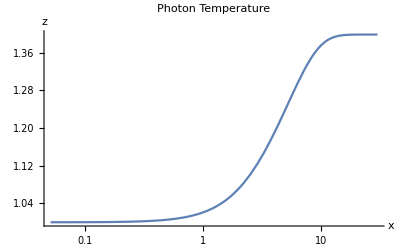

-Graphics-

-Graphics-

```mathematica
(*Non-dimensional photon temperature*)
z0=(11/4.)^(1/3);
zmax=Last[z];
ρνeq=7/8 π^2/15(me/xfin)^4;
(*Exact energy densitiy for νe and νμ*)
ρνe=1/π^2(me/xfin)^4 NIntegrate[ω^3 fνe[ω],{ω,ymin,ymax}];
ρνμ=1/π^2(me/xfin)^4 NIntegrate[ω^3 fνμ[ω],{ω,ymin,ymax}];
(*Non-thermar Distortions to Energy Density*)
δρνe=Abs[ρνe-ρνeq]/ρνeq;
δρνμ=Abs[ρνμ-ρνeq]/ρνeq;
(*From Mangano2005*)
Neff=(z0/zmax)^4(3+δρνe+2δρνμ);

Print[Style["Numerical Results",Red]];
Print["zfin = ",SetPrecision[Max[z],5]];
Print["δρνe = ",SetPrecision[100δρνe,3]];
Print["δρνμ = ",SetPrecision[100δρνμ,3]];
Print["Neff = ",SetPrecision[Neff,4]];
Print[" "];

(*Non-dimensional photon temperature*)
Z=Interpolation[Table[{xin+hx (i-1),z[[i]]},{i,m}]];
LogLinearPlot[Z[X],{X,xin,xfin},PlotRange->All,AxesLabel->{"x","z"},PlotLabel->"Photon Temperature"]

(*Deviation from Equilibrium Spectra*)
LogLinearPlot[{Distfνe[x],Distfνμ[x]},{x,xin,xfin},PlotRange->All,AxesLabel->{"x","fν/fνeq"},PlotLabels->{"fνe","fνμ"},PlotLabel->"Time-dependent Distortions (y=10)"]

(*Momenta-Dependent Distortions*)
M=60;ListLinePlot[{Table[{y1[[i]],fνe[y1[[i]]]/fν0[y1[[i]]]},{i,M}],Table[{y1[[i]],fνμ[y1[[i]]]/fν0[y1[[i]]]},{i,M}]},AxesLabel->{"y","fν/fνeq"},PlotLabels->{"fνe","fνμ"},PlotLabel->"Momenta-dependent Distortions"]
```